```mathematica
threepoints[{x_, y_}] := {{x+r,y},{x-r,y},{x,0}} /. r -> Abs[y]
Relm[x_] := {Re[x],Im[x]}
z1 := 2+2 ⅈ
z2 := 1 + 3 ⅈ
z3 := 2 ⅈ
f[a_,b_] := (z-z1)/(z-z3) (z2-z3)/(z2-z1) /. z -> a + b ⅈ // Relm
g[{q_,p_}] := (z3-z1)/(((z2-z1)/(z2-z3))z-1)+z3 /. z -> q+p ⅈ // Relm
```

```mathematica
(z3-z1)/(((z2-z1)/(z2-z3))z-1)+z3
```

2 ⅈ-2/(-1+ⅈ z)

```mathematica
p1 = {f[1,3],f[2,2],f[1,1]}
p2 = {f[-1,-1],f[-2,0], f[-3,-1]}
p3 =  {f[2,0],f[1,-1],f[3,-1]}
```

{{1,0},{0,0},{-1,0}}

{{-3/5,-6/5},{-1/2,-3/2},{-1/3,-4/3}}

{{-1/2,-1/2},{-3/5,-4/5},{-1/3,-2/3}}

```mathematica
Simplify[g[{(√5+1)/2,-1}]]
Simplify[g[{(√5-1)/2,0}]]
```

{0,1+√5}

{1+1/(√5),2+2/(√5)}

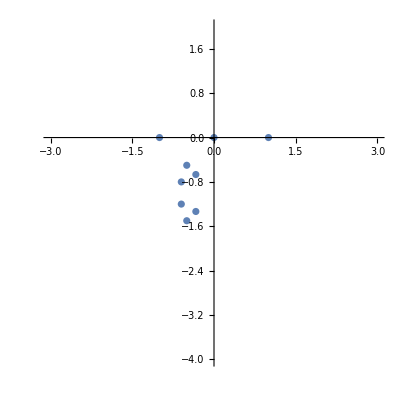

```mathematica
projected = ListPlot[Join[p1,p2,p3],PlotRange -> {{-3,3},{-4,2}},AspectRatio -> 1]
```

```mathematica
eq[{x1_,y1_},{x2_,y2_}] := 2x(x2-x1)+2y(y2-y1) + x1^2+y1^2-x2^2- y2^2 == 0
```

```mathematica
center[pts_] := {x,y} /. First[Solve[eq[pts[[1]],pts[[2]]] && eq[pts[[1]],pts[[3]]],{x,y}]]
dist[{x1_,y1_},{x2_,y2_}] := √((x1-x2)^2+(y1-y2)^2)
circ3[{p1_,p2_,p3_}] := Circle[c, Abs[dist[c,p1]]]  /. c -> center[{p1,p2,p3}]
```

```mathematica
f[-2,-1]
circ3[p2]
f[2,-1]
dist[f[2,-1],#] & /@ p3
circ3[p3]
```

{-6/13,-17/13}

Circle[{-1/2,-4/3},1/6]

{-6/13,-9/13}

{1/(√26),√(2/65),(√(2/13))/3}

Circle[{-1/2,-2/3},1/6]

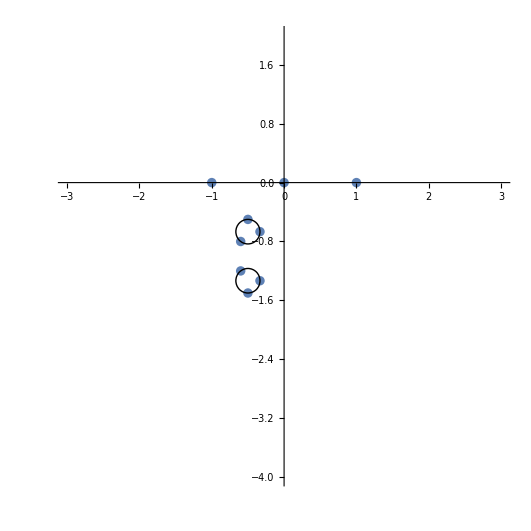

```mathematica
Show[projected,Graphics[circ3[p2]],Graphics[circ3[p3]]]
```

```mathematica
solutions = {x,y} /. Join [Solve[(x+1/2)^2+(y+4/3)^2==(y + 1/6)^2 && (x+1/2)^2+(y+2/3)^2== (y + 1/6)^2,{x,y}],
Solve[(x+1/2)^2+(y+4/3)^2==(y + 1/6)^2 && (x+1/2)^2+(y+2/3)^2== (y - 1/6)^2,{x,y}],
Solve[(x+1/2)^2+(y+4/3)^2==(y - 1/6)^2 && (x+1/2)^2+(y+2/3)^2== (y - 1/6)^2,{x,y}],
Solve[(x+1/2)^2+(y+4/3)^2==(y - 1/6)^2 && (x+1/2)^2+(y+2/3)^2== (y + 1/6)^2,{x,y}]]
```

{{1/6 (-3-√21),-1},{1/6 (-3+√21),-1},{1/6 (-3-√105),-2},{1/6 (-3+√105),-2},{1/2 (-1-√5),-1},{1/2 (-1+√5),-1},{-1,-2/3},{0,-2/3}}

```mathematica
circles := Graphics[Circle[#,Abs[#[[2]]]]] & /@ solutions
```

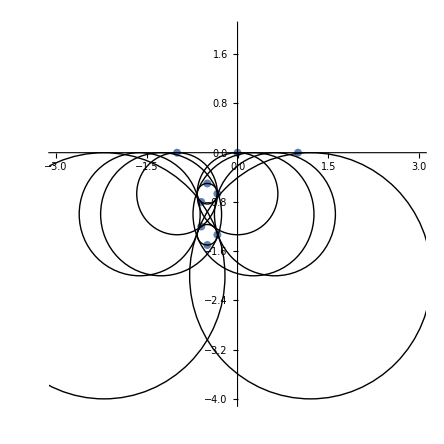

```mathematica
Show[projected, Graphics[circ3[p2]],Graphics[circ3[p3]], circles]
```

```mathematica
solpoints = threepoints[solutions[[1]]];
basepoints = g /@ solpoints;
solcirc = Simplify[circ3[basepoints]]
```

Circle[{0,-2/5 (1+√21)},3/5 (1+√21)]

```mathematica
ShowSolution[sol_] :=
Module[{solpoints,basepoints,solcirc},
solpoints = threepoints[sol];
basepoints = g /@ solpoints;
solcirc = circ3[basepoints];
Show[Graphics[solcirc, Axes -> True],Graphics[Circle[{1,2},1]],Graphics[Circle[{-2,-1},1]],Graphics[Circle[{2,-1},1]]]]
```

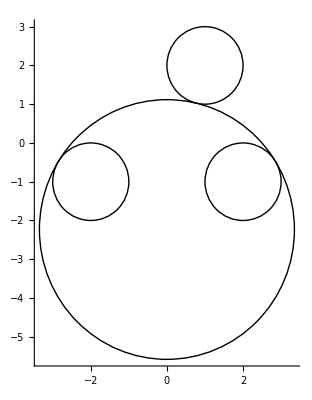
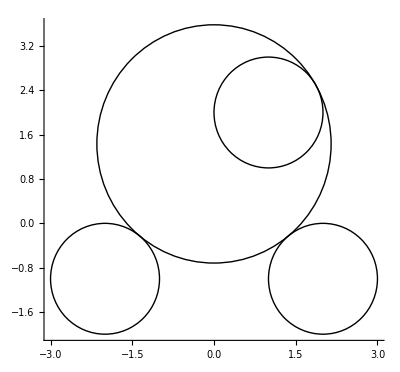
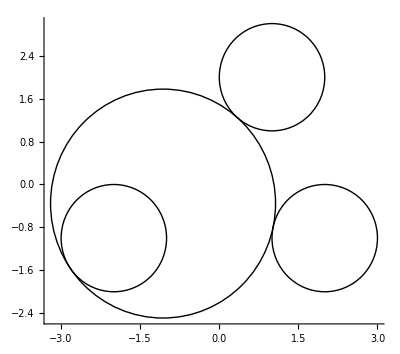
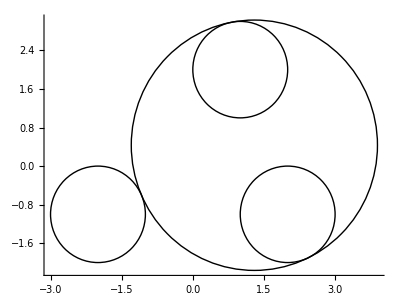
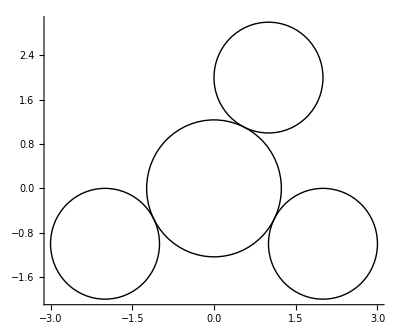
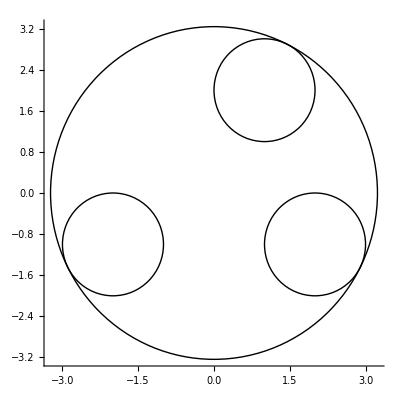
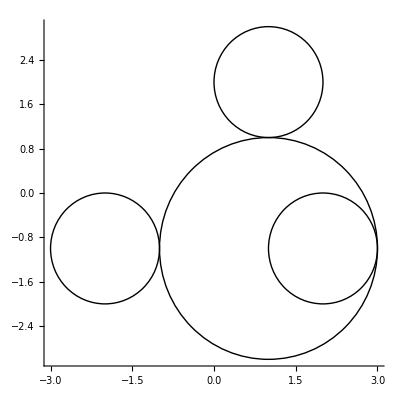
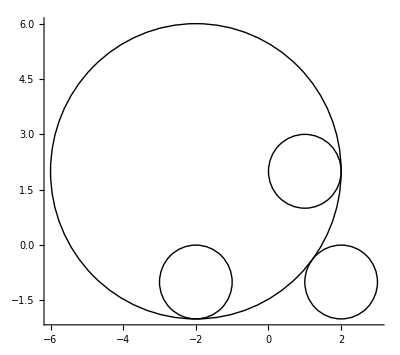

```mathematica
ShowSolution /@ solutions
```